Be aware of the fact that the path to the input files could be different in your case!!!!

## Visualization of the resulting curves

```mathematica
Clear[phi0,phi1,phi2,phi3]
```

### Basic functions Level 1

```mathematica
phi0[1,4,x_]:=0/;x<0
```

```mathematica
phi0[1,4,x_]:=0/;(x≥1/2)
```

```mathematica
phi0[1,4,x_]:=1250/3*x^4/;(0≤x<1/10)
```

```mathematica
phi0[1,4,x_]:=-1/8+5/3*x+25*(x-1/10)^2+500/3*(x-1/10)^3-5000/3*(x-1/10)^4/;(1/10≤x<2/10)
```

```mathematica
phi0[1,4,x_]:=-13/24+5*x-25*(x-1/5)^2-500*(x-1/5)^3+2500*(x-1/5)^4/;(2/10≤x<3/10)
```

```mathematica
phi0[1,4,x_]:=47/24-5*x-25*(x-3/10)^2+500*(x-3/10)^3-5000/3*(x-3/10)^4/;(3/10≤x<4/10)
```

```mathematica
phi0[1,4,x_]:=17/24-5/3*x+25*(x-2/5)^2-500/3*(x-2/5)^3+1250/3*(x-2/5)^4/;(4/10≤x<5/10)
```

```mathematica
phi0[1,i_,x_]:=phi0[1,4,x+(4-i)/10]/;(0≤i≤3)
```

```mathematica
phi0[1,i_,x_]:=phi0[1,4,x-(i-4)/10]/;(5≤i≤13)
```

```mathematica
phi1[1,4,x_]:=0/;x<0
```

```mathematica
phi1[1,4,x_]:=0/;(x≥1/2)
```

```mathematica
phi1[1,4,x_]:=(5000 x^3)/3/;(0≤x<1/10)
```

```mathematica
phi1[1,4,x_]:=5/3+50 (-1/10+x)+500 (-1/10+x)^2-20000/3 (-1/10+x)^3/;(1/10≤x<2/10)
```

```mathematica
phi1[1,4,x_]:=5-50 (-1/5+x)-1500 (-1/5+x)^2+10000 (-1/5+x)^3/;(2/10≤x<3/10)
```

```mathematica
phi1[1,4,x_]:=-5-50 (-3/10+x)+1500 (-3/10+x)^2-20000/3 (-3/10+x)^3/;(3/10≤x<4/10)
```

```mathematica
phi1[1,4,x_]:=-5/3+50 (-2/5+x)-500 (-2/5+x)^2+5000/3 (-2/5+x)^3/;(4/10≤x<5/10)
```

```mathematica
phi1[1,i_,x_]:=phi1[1,4,x+(4-i)/10]/;(0≤i≤3)
```

```mathematica
phi1[1,i_,x_]:=phi1[1,4,x-(i-4)/10]/;(5≤i≤13)
```

```mathematica
phi2[1,4,x_]:=0/;x<0
```

```mathematica
phi2[1,4,x_]:=0/;(x≥1/2)
```

```mathematica
phi2[1,4,x_]:=5000 x^2/;(0≤x<1/10)
```

```mathematica
phi2[1,4,x_]:=50+1000 (-1/10+x)-20000 (-1/10+x)^2/;(1/10≤x<2/10)
```

```mathematica
phi2[1,4,x_]:=-50-3000 (-1/5+x)+30000 (-1/5+x)^2/;(2/10≤x<3/10)
```

```mathematica
phi2[1,4,x_]:=-50+3000 (-3/10+x)-20000 (-3/10+x)^2/;(3/10≤x<4/10)
```

```mathematica
phi2[1,4,x_]:=50-1000 (-2/5+x)+5000 (-2/5+x)^2/;(4/10≤x<5/10)
```

```mathematica
phi2[1,i_,x_]:=phi2[1,4,x+(4-i)/10]/;(0≤i≤3)
```

```mathematica
phi2[1,i_,x_]:=phi2[1,4,x-(i-4)/10]/;(5≤i≤13)
```

```mathematica
phi3[1,4,x_]:=0/;x<0
```

```mathematica
phi3[1,4,x_]:=0/;(x≥1/2)
```

```mathematica
phi3[1,4,x_]:=10000 x/;(0≤x<1/10)
```

```mathematica
phi3[1,4,x_]:=1000-40000 (-1/10+x)/;(1/10≤x<2/10)
```

```mathematica
phi3[1,4,x_]:=-3000+60000 (-1/5+x)/;(2/10≤x<3/10)
```

```mathematica
phi3[1,4,x_]:=3000-40000 (-3/10+x)/;(3/10≤x<4/10)
```

```mathematica
phi3[1,4,x_]:=-1000+10000 (-2/5+x)/;(4/10≤x<5/10)
```

```mathematica
phi3[1,i_,x_]:=phi3[1,4,x+(4-i)/10]/;(0≤i≤3)
```

```mathematica
phi3[1,i_,x_]:=phi3[1,4,x-(i-4)/10]/;(5≤i≤13)
```

### Basic functions Level 2

```mathematica
phi0[2,4,x_]:=0/;x<0
```

```mathematica
phi0[2,4,x_]:=0/;(x≥1/4)
```

```mathematica
phi0[2,4,x_]:=20000/3*x^4/;(0≤x<1/20)
```

```mathematica
phi0[2,4,x_]:=-1/8+10/3*x+100*(x-1/20)^2+4000/3*(x-1/20)^3-80000/3*(x-1/20)^4/;(1/20≤x<2/20)
```

```mathematica
phi0[2,4,x_]:=-13/24+10*x-100*(x-1/10)^2-4000*(x-1/10)^3+40000*(x-1/10)^4/;(2/20≤x<3/20)
```

```mathematica
phi0[2,4,x_]:=47/24-10*x-100*(x-3/20)^2+4000*(x-3/20)^3-80000/3*(x-3/20)^4/;(3/20≤x<4/20)
```

```mathematica
phi0[2,4,x_]:=17/24-10/3*x+100*(x-1/5)^2-4000/3*(x-1/5)^3+20000/3*(x-1/5)^4/;(4/20≤x<5/20)
```

```mathematica
phi0[2,i_,x_]:=phi0[2,4,x+(4-i)/20]/;(0≤i≤3)
```

```mathematica
phi0[2,i_,x_]:=phi0[2,4,x-(i-4)/20]/;(5≤i≤23)
```

```mathematica
phi1[2,4,x_]:=0/;x<0
```

```mathematica
phi1[2,4,x_]:=0/;(x≥1/4)
```

```mathematica
phi1[2,4,x_]:=(80000 x^3)/3/;(0≤x<1/20)
```

```mathematica
phi1[2,4,x_]:=10/3+200 (-1/20+x)+4000 (-1/20+x)^2-320000/3 (-1/20+x)^3/;(1/20≤x<2/20)
```

```mathematica
phi1[2,4,x_]:=10-200 (-1/10+x)-12000 (-1/10+x)^2+160000 (-1/10+x)^3/;(2/20≤x<3/20)
```

```mathematica
phi1[2,4,x_]:=-10-200 (-3/20+x)+12000 (-3/20+x)^2-320000/3 (-3/20+x)^3/;(3/20≤x<4/20)
```

```mathematica
phi1[2,4,x_]:=-10/3+200 (-1/5+x)-4000 (-1/5+x)^2+80000/3 (-1/5+x)^3/;(4/20≤x<5/20)
```

```mathematica
phi1[2,i_,x_]:=phi1[2,4,x+(4-i)/20]/;(0≤i≤3)
```

```mathematica
phi1[2,i_,x_]:=phi1[2,4,x-(i-4)/20]/;(5≤i≤23)
```

```mathematica
phi2[2,4,x_]:=0/;x<0
```

```mathematica
phi2[2,4,x_]:=0/;(x≥1/4)
```

```mathematica
phi2[2,4,x_]:=80000 x^2/;(0≤x<1/20)
```

```mathematica
phi2[2,4,x_]:=200+8000 (-1/20+x)-320000 (-1/20+x)^2/;(1/20≤x<2/20)
```

```mathematica
phi2[2,4,x_]:=-200-24000 (-1/10+x)+480000 (-1/10+x)^2/;(2/20≤x<3/20)
```

```mathematica
phi2[2,4,x_]:=-200+24000 (-3/20+x)-320000 (-3/20+x)^2/;(3/20≤x<4/20)
```

```mathematica
phi2[2,4,x_]:=200-8000 (-1/5+x)+80000 (-1/5+x)^2/;(4/20≤x<5/20)
```

```mathematica
phi2[2,i_,x_]:=phi2[2,4,x+(4-i)/20]/;(0≤i≤3)
```

```mathematica
phi2[2,i_,x_]:=phi2[2,4,x-(i-4)/20]/;(5≤i≤23)
```

```mathematica
phi3[2,4,x_]:=0/;x<0
```

```mathematica
phi3[2,4,x_]:=0/;(x≥1/4)
```

```mathematica
phi3[2,4,x_]:=160000 x/;(0≤x<1/20)
```

```mathematica
phi3[2,4,x_]:=8000-640000 (-1/20+x)/;(1/20≤x<2/20)
```

```mathematica
phi3[2,4,x_]:=-24000+960000 (-1/10+x)/;(2/20≤x<3/20)
```

```mathematica
phi3[2,4,x_]:=24000-640000 (-3/20+x)/;(3/20≤x<4/20)
```

```mathematica
phi3[2,4,x_]:=-8000+160000 (-1/5+x)/;(4/20≤x<5/20)
```

```mathematica
phi3[2,i_,x_]:=phi3[2,4,x+(4-i)/20]/;(0≤i≤3)
```

```mathematica
phi3[2,i_,x_]:=phi3[2,4,x-(i-4)/20]/;(5≤i≤23)
```

### Basic functions Level 3

```mathematica
phi0[3,4,x_]:=0/;x<0
```

```mathematica
phi0[3,4,x_]:=0/;(x≥1/8)
```

```mathematica
phi0[3,4,x_]:=320000/3*x^4/;(0≤x<1/40)
```

```mathematica
phi0[3,4,x_]:=-1/8+20/3*x+400*(x-1/40)^2+32000/3*(x-1/40)^3-1280000/3*(x-1/40)^4/;(1/40≤x<2/40)
```

```mathematica
phi0[3,4,x_]:=-13/24+20*x-400*(x-1/20)^2-32000*(x-1/20)^3+640000*(x-1/20)^4/;(2/40≤x<3/40)
```

```mathematica
phi0[3,4,x_]:=47/24-20*x-400*(x-3/40)^2+32000*(x-3/40)^3-1280000/3*(x-3/40)^4/;(3/40≤x<4/40)
```

```mathematica
phi0[3,4,x_]:=17/24-20/3*x+400*(x-1/10)^2-32000/3*(x-1/10)^3+320000/3*(x-1/10)^4/;(4/40≤x<5/40)
```

```mathematica
phi0[3,i_,x_]:=phi0[3,4,x+(4-i)/40]/;(0≤i≤3)
```

```mathematica
phi0[3,i_,x_]:=phi0[3,4,x-(i-4)/40]/;(5≤i≤43)
```

```mathematica
phi1[3,4,x_]:=0/;x<0
```

```mathematica
phi1[3,4,x_]:=0/;(x≥1/8)
```

```mathematica
phi1[3,4,x_]:=(1280000 x^3)/3/;(0≤x<1/40)
```

```mathematica
phi1[3,4,x_]:=20/3+800 (-1/40+x)+32000 (-1/40+x)^2-5120000/3 (-1/40+x)^3/;(1/40≤x<2/40)
```

```mathematica
phi1[3,4,x_]:=20-800 (-1/20+x)-96000 (-1/20+x)^2+2560000 (-1/20+x)^3/;(2/40≤x<3/40)
```

```mathematica
phi1[3,4,x_]:=-20-800 (-3/40+x)+96000 (-3/40+x)^2-5120000/3 (-3/40+x)^3/;(3/40≤x<4/40)
```

```mathematica
phi1[3,4,x_]:=-20/3+800 (-1/10+x)-32000 (-1/10+x)^2+1280000/3 (-1/10+x)^3/;(4/40≤x<5/40)
```

```mathematica
phi1[3,i_,x_]:=phi1[3,4,x+(4-i)/40]/;(0≤i≤3)
```

```mathematica
phi1[3,i_,x_]:=phi1[3,4,x-(i-4)/40]/;(5≤i≤43)
```

```mathematica
phi2[3,4,x_]:=0/;x<0
```

```mathematica
phi2[3,4,x_]:=0/;(x≥1/8)
```

```mathematica
phi2[3,4,x_]:=1280000 x^2/;(0≤x<1/40)
```

```mathematica
phi2[3,4,x_]:=800+64000 (-1/40+x)-5120000 (-1/40+x)^2/;(1/40≤x<2/40)
```

```mathematica
phi2[3,4,x_]:=-800-192000 (-1/20+x)+7680000 (-1/20+x)^2/;(2/40≤x<3/40)
```

```mathematica
phi2[3,4,x_]:=-800+192000 (-3/40+x)-5120000 (-3/40+x)^2/;(3/40≤x<4/40)
```

```mathematica
phi2[3,4,x_]:=800-64000 (-1/10+x)+1280000 (-1/10+x)^2/;(4/40≤x<5/40)
```

```mathematica
phi2[3,i_,x_]:=phi2[3,4,x+(4-i)/40]/;(0≤i≤3)
```

```mathematica
phi2[3,i_,x_]:=phi2[3,4,x-(i-4)/40]/;(5≤i≤43)
```

```mathematica
phi3[3,4,x_]:=0/;x<0
```

```mathematica
phi3[3,4,x_]:=0/;(x≥1/8)
```

```mathematica
phi3[3,4,x_]:=2560000 x/;(0≤x<1/40)
```

```mathematica
phi3[3,4,x_]:=64000-10240000 (-1/40+x)/;(1/40≤x<2/40)
```

```mathematica
phi3[3,4,x_]:=-192000+15360000 (-1/20+x)/;(2/40≤x<3/40)
```

```mathematica
phi3[3,4,x_]:=192000-10240000 (-3/40+x)/;(3/40≤x<4/40)
```

```mathematica
phi3[3,4,x_]:=-64000+2560000 (-1/10+x)/;(4/40≤x<5/40)
```

```mathematica
phi3[3,i_,x_]:=phi3[3,4,x+(4-i)/40]/;(0≤i≤3)
```

```mathematica
phi3[3,i_,x_]:=phi3[3,4,x-(i-4)/40]/;(5≤i≤43)
```

### Basic functions Level 4

```mathematica
phi0[4,4,x_]:=phi0[3,4,2*x]
```

```mathematica
phi0[4,i_,x_]:=phi0[4,4,x+(4-i)/80]/;(0≤i≤3)
```

```mathematica
phi0[4,i_,x_]:=phi0[4,4,x-(i-4)/80]/;(5≤i≤83)
```

```mathematica
phi1[4,4,x_]:=2*phi1[3,4,2*x]
```

```mathematica
phi1[4,i_,x_]:=phi1[4,4,x+(4-i)/80]/;(0≤i≤3)
```

```mathematica
phi1[4,i_,x_]:=phi1[4,4,x-(i-4)/80]/;(5≤i≤83)
```

```mathematica
phi2[4,4,x_]:=4*phi2[3,4,2*x]
```

```mathematica
phi2[4,i_,x_]:=phi2[4,4,x+(4-i)/80]/;(0≤i≤3)
```

```mathematica
phi2[4,i_,x_]:=phi2[4,4,x-(i-4)/80]/;(5≤i≤83)
```

```mathematica
phi3[4,4,x_]:=8*phi3[3,4,2*x]
```

```mathematica
phi3[4,i_,x_]:=phi3[4,4,x+(4-i)/80]/;(0≤i≤3)
```

```mathematica
phi3[4,i_,x_]:=phi3[4,4,x-(i-4)/80]/;(5≤i≤83)
```

```mathematica
(D[phi0[4,4,x],x])/.x->3
```

2 phi0^(0,0,1)[3,4,6]

### Basic functions Level 5

```mathematica
phi0[5,4,x_]:=phi0[4,4,2*x]
```

```mathematica
phi0[5,i_,x_]:=phi0[5,4,x+(4-i)/160]/;(0≤i≤3)
```

```mathematica
phi0[5,i_,x_]:=phi0[5,4,x-(i-4)/160]/;(5≤i≤163)
```

```mathematica
phi1[5,4,x_]:=2*phi1[4,4,2*x]
```

```mathematica
phi1[5,i_,x_]:=phi1[5,4,x+(4-i)/160]/;(0≤i≤3)
```

```mathematica
phi1[5,i_,x_]:=phi1[5,4,x-(i-4)/160]/;(5≤i≤163)
```

```mathematica
phi2[5,4,x_]:=4*phi2[4,4,2*x]
```

```mathematica
phi2[5,i_,x_]:=phi2[5,4,x+(4-i)/160]/;(0≤i≤3)
```

```mathematica
phi2[5,i_,x_]:=phi2[5,4,x-(i-4)/160]/;(5≤i≤163)
```

```mathematica
phi3[5,4,x_]:=8*phi3[4,4,2*x]
```

```mathematica
phi3[5,i_,x_]:=phi3[5,4,x+(4-i)/160]/;(0≤i≤3)
```

```mathematica
phi3[5,i_,x_]:=phi3[5,4,x-(i-4)/160]/;(5≤i≤163)
```

### Curve definition Level 2

```mathematica
(*curve0[t_,coe_]:=∑_(i=0)^23 coe⟦i+1⟧*phi0[2,i,t]
curve1[t_,coe_]:=∑_(i=0)^23 coe⟦i+1⟧*phi1[2,i,t]
curve2[t_,coe_]:=∑_(i=0)^23 coe⟦i+1⟧*phi2[2,i,t]
curve3[t_,coe_]:=∑_(i=0)^23 coe⟦i+1⟧*phi3[2,i,t]*)
```

```mathematica
Int[g_,a_,b_,num_]:=(b-a)/(num+1)*(∑_(i=0)^num √((g/.t->(i+0.0)/num)^2))
```

### Curve definition Level 3

```mathematica
(*curve0[t_,coe_]:=∑_(i=0)^43 coe⟦i+1⟧*phi0[3,i,t]
curve1[t_,coe_]:=∑_(i=0)^43 coe⟦i+1⟧*phi1[3,i,t]
curve2[t_,coe_]:=∑_(i=0)^43 coe⟦i+1⟧*phi2[3,i,t]
curve3[t_,coe_]:=∑_(i=0)^43 coe⟦i+1⟧*phi3[3,i,t]*)
```

```mathematica
Int[g_,a_,b_,num_]:=(b-a)/(num+1)*(∑_(i=0)^num √((g/.t->(i+0.0)/num)^2))
```

### Curve definition Level 4

```mathematica
curve0[t_,coe_]:=∑_(i=0)^83 coe⟦i+1⟧*phi0[4,i,t]
curve1[t_,coe_]:=∑_(i=0)^83 coe⟦i+1⟧*phi1[4,i,t]
curve2[t_,coe_]:=∑_(i=0)^83 coe⟦i+1⟧*phi2[4,i,t]
curve3[t_,coe_]:=∑_(i=0)^83 coe⟦i+1⟧*phi3[4,i,t]
```

```mathematica
Int[g_,a_,b_,num_]:=(b-a)/(num+1)*(∑_(i=0)^num √((g/.t->(i+0.0)/num)^2))
```

### Curve definition Level 5

```mathematica
(*curve0[t_,coe_]:=∑_(i=0)^163 coe⟦i+1⟧*phi0[5,i,t]
curve1[t_,coe_]:=∑_(i=0)^163 coe⟦i+1⟧*phi1[5,i,t]
curve2[t_,coe_]:=∑_(i=0)^163 coe⟦i+1⟧*phi2[5,i,t]
curve3[t_,coe_]:=∑_(i=0)^163 coe⟦i+1⟧*phi3[5,i,t]*)
```

```mathematica
Int[g_,a_,b_,num_]:=(b-a)/(num+1)*(∑_(i=0)^num √((g/.t->(i+0.0)/num)^2))
```

```mathematica
ComputeExtrema[num_,function_]:=Module[{count=0,values},For[i=0,i<num,i++,values={function/.t->Mod[i,num]/num,function/.t->Mod[i+1,num]/num,function/.t->Mod[i+2,num]/num};
If[(values⟦1⟧<values⟦2⟧&&values⟦3⟧<values⟦2⟧)||(values⟦1⟧>values⟦2⟧&&values⟦3⟧>values⟦2⟧),count++,]];count]
```

```mathematica
num=1000;
```

```mathematica
lamda=4;
```

### Initial curve

```mathematica
coeffInit=ReadList["Documents/GISMO/build/filedata/output_init.txt"]⟦1⟧
```

{{2.45721,9.6077},{3.01677,8.80152},{3.26904,8.01281},{3.27712,7.09435},{3.51124,6.62149},{3.83394,5.96271},{3.87859,5.5221},{4.51618,4.7812},{4.98728,4.04253},{5.28657,3.89849},{6.03659,4.0216},{6.44236,3.66632},{7.44344,3.15685},{8.21778,3.01401},{8.52868,3.14327},{9.33401,2.44388},{9.97565,2.09874},{10.4036,1.71283},{10.381,0.941093},{10.8418,0.585144},{10.5336,-0.563542},{10.3919,-1.09577},{10.3186,-1.91209},{9.60067,-2.09685},{8.97742,-2.9295},{8.55399,-2.88547},{8.1042,-3.22003},{6.77544,-3.17819},{6.16839,-3.43127},{5.41795,-3.42539},{5.10688,-3.46338},{3.98953,-3.14998},{3.29085,-2.73852},{2.65744,-2.60382},{1.63758,-2.65962},{0.614188,-2.95736},{-0.380067,-2.70005},{-1.64409,-2.84024},{-2.27997,-3.11791},{-3.47931,-2.84839},{-4.12922,-2.91398},{-4.57968,-3.20347},{-5.54743,-3.11389},{-6.2071,-3.5449},{-7.31601,-3.05389},{-7.65633,-3.37741},{-8.67899,-3.17082},{-9.47872,-2.931},{-9.70791,-2.13171},{-9.97022,-1.54857},{-10.2237,-0.938799},{-10.4881,-0.578305},{-10.6405,0.657995},{-10.3546,1.1986},{-10.0098,1.58126},{-10.1408,2.34975},{-9.19114,2.63631},{-8.9208,2.9799},{-8.10707,3.02862},{-7.57607,3.28081},{-6.42339,3.48573},{-6.05199,3.70945},{-4.99544,4.03507},{-4.64863,4.16549},{-4.25649,4.80013},{-3.70502,5.33524},{-3.62237,5.85442},{-3.32126,6.93198},{-3.1742,7.08217},{-3.14966,8.14428},{-3.06635,9.00784},{-2.69781,9.25682},{-2.21991,9.88032},{-1.87747,10.4509},{-0.988928,10.7292},{-0.282346,10.6396},{0.129661,10.471},{1.2051,10.7509},{1.67899,10.4653},{2.46112,10.1287},{2.45721,9.6077},{3.01677,8.80152},{3.26904,8.01281},{3.27712,7.09435}}

```mathematica
fInit[t_]:=curve0[t,coeffInit]
```

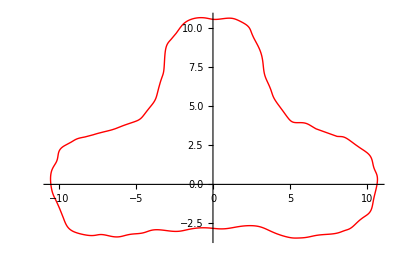

```mathematica
plCurveInit=ParametricPlot[fInit[t],{t,0,1},PlotRange->All,PlotStyle->Red]
```

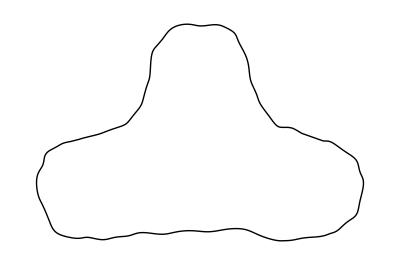

```mathematica
plCurveInitBlack=ParametricPlot[fInit[t],{t,0,1},PlotRange->All,PlotStyle->Black,Axes->False]
```

```mathematica
Export["fairing_init.eps",Show[plCurveInitBlack]]
```

fairing_init.eps

```mathematica
(*points=Table[fInit[i/2000.0],{i,0,1999}];
parameters=Table[i/(Length[points]+0.0),{i,0,Length[points]-1}];
Export["PointCloud.txt",points]
Export["Parameter.txt",Table[i/(Length[points]+0.0),{i,0,Length[points]-1}]]*)
```

```mathematica
hInit0[t_]:=curve0[t,coeffInit];
hInit1[t_]:=curve1[t,coeffInit];
hInit2[t_]:=curve2[t,coeffInit];
hInit3[t_]:=curve3[t,coeffInit];
kInit0=hInit0[t];
kInit1=hInit1[t];
kInit2=hInit2[t];
kInit3=hInit3[t];

KappaInit=(kInit1⟦1⟧*kInit2⟦2⟧-kInit2⟦1⟧*kInit1⟦2⟧)/((kInit1⟦1⟧^2+kInit1⟦2⟧^2)^(3/2));
```

```mathematica
ComputeExtrema[num,KappaInit]
```

66

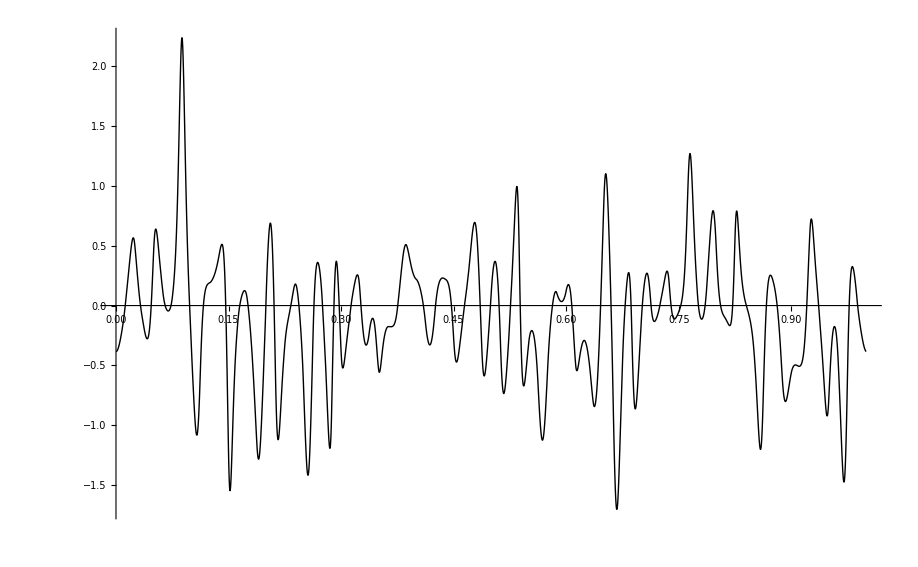

```mathematica
CurvaturePlotInit=Plot[KappaInit,{t,0,1},PlotStyle->Black,PlotRange->All]
```

```mathematica
Export["curvatureInit.eps",Show[CurvaturePlotInit]]
```

curvatureInit.eps

### Variation curve

```mathematica
coeffVariation=ReadList["Documents/GISMO/build/filedata/output_variation.txt"]⟦1⟧
```

{{2.45721,9.6077},{3.01677,8.80152},{3.26904,8.01281},{3.27712,7.09435},{3.51124,6.62149},{3.83394,5.96271},{3.87859,5.5221},{4.51618,4.7812},{4.98728,4.04253},{5.28657,3.89849},{6.03659,4.0216},{6.44236,3.66632},{7.44344,3.15685},{8.21778,3.01401},{8.52868,3.14327},{9.33401,2.44388},{9.97565,2.09874},{10.4036,1.71283},{10.381,0.941093},{10.8418,0.585144},{10.5336,-0.563542},{10.3919,-1.09577},{10.3186,-1.91209},{9.60067,-2.09685},{8.97742,-2.9295},{8.55399,-2.88547},{8.1042,-3.22003},{6.77544,-3.17819},{6.16839,-3.43127},{5.41795,-3.42539},{5.10688,-3.46338},{3.98953,-3.14998},{3.29085,-2.73852},{2.65744,-2.60382},{1.63758,-2.65962},{0.614188,-2.95736},{-0.380067,-2.70005},{-1.64409,-2.84024},{-2.27997,-3.11791},{-3.47931,-2.84839},{-4.12922,-2.91398},{-4.57968,-3.20347},{-5.54743,-3.11389},{-6.2071,-3.5449},{-7.31601,-3.05389},{-7.65633,-3.37741},{-8.67899,-3.17082},{-9.47872,-2.931},{-9.70791,-2.13171},{-9.97022,-1.54857},{-10.2237,-0.938799},{-10.4881,-0.578305},{-10.6405,0.657995},{-10.3546,1.1986},{-10.0098,1.58126},{-10.1408,2.34975},{-9.19114,2.63631},{-8.9208,2.9799},{-8.10707,3.02862},{-7.57607,3.28081},{-6.42339,3.48573},{-6.05199,3.70945},{-4.99544,4.03507},{-4.64863,4.16549},{-4.25649,4.80013},{-3.70502,5.33524},{-3.62237,5.85442},{-3.32126,6.93198},{-3.1742,7.08217},{-3.14966,8.14428},{-3.06635,9.00784},{-2.69781,9.25682},{-2.21991,9.88032},{-1.87747,10.4509},{-0.988928,10.7292},{-0.282346,10.6396},{0.129661,10.471},{1.2051,10.7509},{1.67899,10.4653},{2.46112,10.1287},{2.45721,9.6077},{3.01677,8.80152},{3.26904,8.01281},{3.27712,7.09435}}

```mathematica
Export["variation.txt",coeffVariation]
```

variation.txt

```mathematica
fVariation[t_]:=curve0[t,coeffVariation]
```

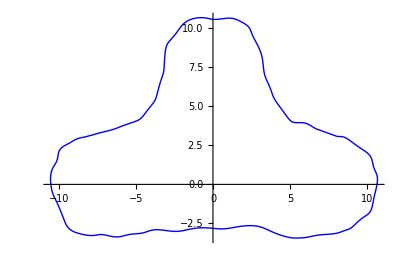

```mathematica
plCurveVariation=ParametricPlot[fVariation[t],{t,0,1},PlotRange->All,PlotStyle->Blue]
```

```mathematica
plCurveVariationBlack=ParametricPlot[fVariation[t],{t,0,1},PlotRange->All,PlotStyle->Black,Axes->False]
```

-Graphics-

```mathematica
Export["fairing_variation.eps",Show[plCurveVariationBlack]]
```

fairing_variation.eps

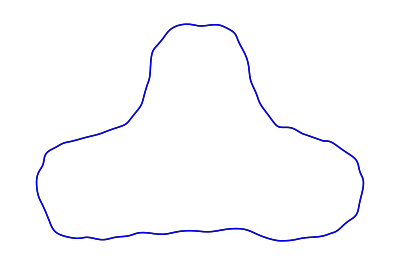

```mathematica
Show[plCurveInitBlack,plCurveVariation]
```

```mathematica
hVariation0[t_]:=curve0[t,coeffVariation];
hVariation1[t_]:=curve1[t,coeffVariation];
hVariation2[t_]:=curve2[t,coeffVariation];
hVariation3[t_]:=curve3[t,coeffVariation];
kVariation0=hVariation0[t];
kVariation1=hVariation1[t];
kVariation2=hVariation2[t];
kVariation3=hVariation3[t];

KappaVariation=(kVariation1⟦1⟧*kVariation2⟦2⟧-kVariation2⟦1⟧*kVariation1⟦2⟧)/((kVariation1⟦1⟧^2+kVariation1⟦2⟧^2)^(3/2));
```

```mathematica
ComputeExtrema[num,KappaVariation]
```

66

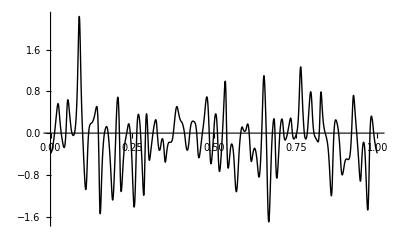

```mathematica
CurvaturePlotVariation=Plot[KappaVariation,{t,0,1},PlotStyle->Black,PlotRange->All]
```

```mathematica
Export["curvatureVariation.eps",Show[CurvaturePlotVariation]]
```

curvatureVariation.eps

```mathematica
fDiffVariation[t_]:=fVariation[t]+lamda*(fInit[t]-fVariation[t])
```

```mathematica
plCurveDiffVariation=ParametricPlot[fDiffVariation[t],{t,0,1},PlotRange->All,PlotStyle->Blue]
```

-Graphics-

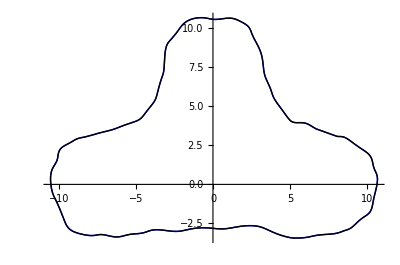

```mathematica
plPaperVariation=Show[plCurveDiffVariation,plCurveVariationBlack]
```

```mathematica
Export["porcupineVariation.eps",Show[plPaperVariation]]
```

porcupineVariation.eps

### Hadenfeld curve

```mathematica
coeffHaden=ReadList["Documents/GISMO/build/filedata/output_haden.txt"]⟦1⟧
```

{{2.62084,9.56961},{2.90935,8.81279},{3.16229,7.99179},{3.37495,7.23092},{3.54102,6.61476},{3.73496,6.05089},{4.02748,5.44428},{4.46061,4.75293},{4.95128,4.20663},{5.42113,3.9922},{5.94728,3.8793},{6.60318,3.61773},{7.37176,3.3088},{8.07925,3.10905},{8.62547,3.00596},{9.27897,2.60261},{9.83216,2.14103},{10.2609,1.62426},{10.5109,1.04759},{10.7307,0.459064},{10.5928,-0.406307},{10.4678,-1.17596},{10.1868,-1.80785},{9.62537,-2.26302},{9.04063,-2.77384},{8.57576,-3.02514},{7.95635,-3.14026},{6.92899,-3.24635},{6.15638,-3.40396},{5.54384,-3.50007},{4.94333,-3.42497},{4.15468,-3.11915},{3.36035,-2.85619},{2.52869,-2.71174},{1.62844,-2.71497},{0.635063,-2.79066},{-0.441002,-2.85629},{-1.49683,-2.92109},{-2.41824,-3.02249},{-3.35015,-2.95582},{-4.07176,-2.99364},{-4.72468,-3.11863},{-5.46417,-3.25981},{-6.27139,-3.38969},{-7.19864,-3.17409},{-7.8034,-3.2962},{-8.61454,-3.16459},{-9.36326,-2.80896},{-9.80435,-2.26927},{-10.0723,-1.68199},{-10.3075,-1.08439},{-10.5059,-0.411247},{-10.5663,0.507234},{-10.3855,1.16144},{-10.1311,1.69756},{-9.98659,2.28311},{-9.35529,2.67207},{-8.75737,2.94101},{-8.11234,3.12922},{-7.40901,3.29849},{-6.59111,3.49544},{-5.88403,3.71304},{-5.14188,3.95275},{-4.55645,4.27362},{-4.11137,4.71547},{-3.77817,5.30255},{-3.52765,5.99317},{-3.338,6.76482},{-3.20149,7.24794},{-3.14006,8.02933},{-3.01918,8.8466},{-2.71203,9.42422},{-2.27436,9.96486},{-1.7261,10.378},{-1.09799,10.6014},{-0.445838,10.601},{0.270512,10.5625},{1.07669,10.6426},{1.77163,10.5014},{2.29316,10.1328},{2.62084,9.56961},{2.90935,8.81279},{3.16229,7.99179},{3.37495,7.23092}}

```mathematica
Length[coeffHaden]
```

84

```mathematica
fHaden[t_]:=curve0[t,coeffHaden]
```

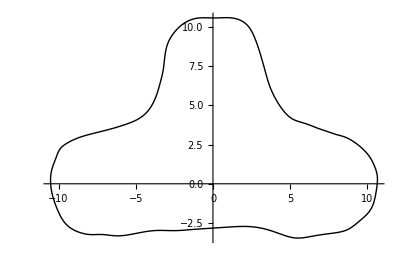

```mathematica
plCurveHaden=ParametricPlot[fHaden[t],{t,0,1},PlotRange->All,PlotStyle->Black]
```

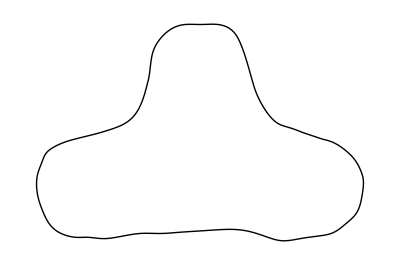

```mathematica
plCurveHadenBlack=ParametricPlot[fHaden[t],{t,0,1},PlotRange->All,PlotStyle->Black,Axes->False]
```

```mathematica
Export["fairing_haden.eps",Show[plCurveHadenBlack]]
```

fairing_haden.eps

```mathematica
hHaden0[t_]:=curve0[t,coeffHaden];
hHaden1[t_]:=curve1[t,coeffHaden];
hHaden2[t_]:=curve2[t,coeffHaden];
hHaden3[t_]:=curve3[t,coeffHaden];
kHaden0=hHaden0[t];
kHaden1=hHaden1[t];
kHaden2=hHaden2[t];
kHaden3=hHaden3[t];

KappaHaden=(kHaden1⟦1⟧*kHaden2⟦2⟧-kHaden2⟦1⟧*kHaden1⟦2⟧)/((kHaden1⟦1⟧^2+kHaden1⟦2⟧^2)^(3/2));
```

```mathematica
ComputeExtrema[num,KappaHaden]
```

44

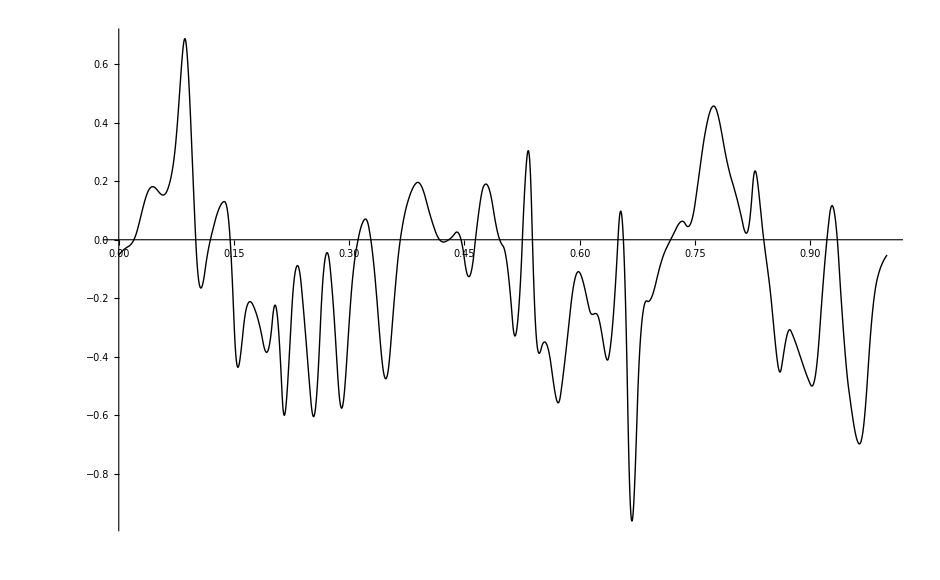

```mathematica
CurvaturePlotHaden=Plot[KappaHaden,{t,0,1},PlotStyle->Black,PlotRange->All]
```

```mathematica
Export["curvatureHaden.eps",Show[CurvaturePlotHaden]]
```

curvatureHaden.eps

```mathematica
fDiffHaden[t_]:=fHaden[t]+lamda*(fInit[t]-fHaden[t])
```

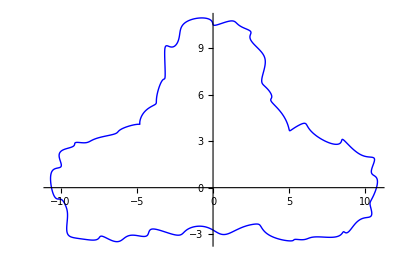

```mathematica
plCurveDiffHaden=ParametricPlot[fDiffHaden[t],{t,0,1},PlotRange->All,PlotStyle->Blue]
```

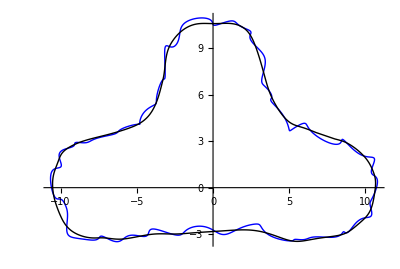

```mathematica
plPaperHaden=Show[plCurveDiffHaden,plCurveHadenBlack]
```

```mathematica
Export["porcupineHaden.eps",Show[plPaperHaden]]
```

porcupineHaden.eps